# The temperature dependence of resistance - Experiment 24

```mathematica
<<CurveFit`
```

CurveFit for Mathematica v7.x thru v11.x, Version 1.96, 4/4/2018

Caltech Sophomore Physics Labs, Pasadena, CA

## Estimating uncertainties due to noise

We estimate the uncertainties due to noise (random errors) in our measurements using the (standard deviation) in our room temperature measurement data.

### Uncertainty in temperature

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 24/room_temp_1.dat

File comment header:

Resistivity Experiment v3.0

Data Acquisition Unit: Agilent Model 34970A
Start Time: 1:38:51.915 PM 5/24/2018 ; Start Temp: 298.9860 K
Time (s)   Temp (K)         R1         R2         R3         R4         R5

Read 341 data points.

We observe that our room temperature measurement of temperature shows a decreasing trend. This is most likely due to a remaining temperature gradient between the lab temperature and the dielectric fluid temperature from the previous experiment carried out using the setup. To estimate the noise level in temperature measurements, we perform a quadratic fit on our data (it qualitatively appears to fit the decrease in temperature relatively well over our range of measurements) and use the standard deviation of the fit as an estimate of noise in our temperature measurements.

```mathematica
QuadraticFit[]
```

n = 341

y(x) = a + b x + c x^2

Fit of (x,y)  (unweighted)

a= 
298.986 | b= 
-0.000094645 | c= 
4.15736×10^-8 | 
σ_a= 
0.000141381 | σ_b= 
1.2788×10^-6 | σ_c= 
2.42319×10^-9 | Std. deviation= 
0.000880185

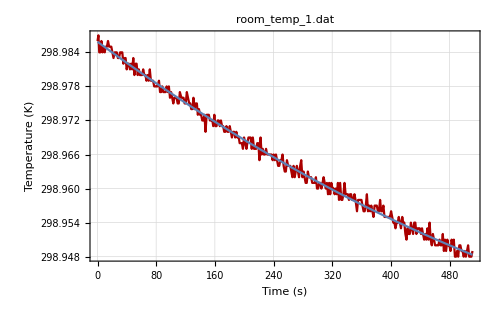
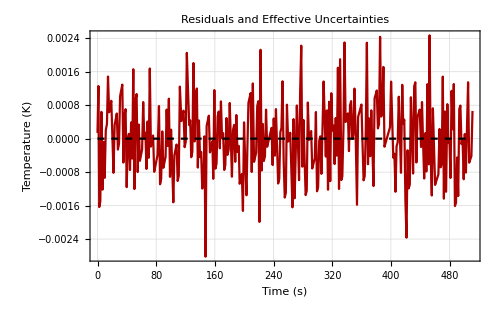
-Graphics-
-Graphics-
y(x) = a + b x + c x^2
a= 
298.986 | b= 
-0.000094645 | c= 
4.15736×10^-8 | 
σ_a= 
0.000141381 | σ_b= 
1.2788×10^-6 | σ_c= 
2.42319×10^-9 | Std. deviation= 
0.000880185

```mathematica
LinearDifferencePlot[FrameLabel->{"Time (s)", "Temperature (K)"}]
```

```mathematica
errTemp=0.0008801846325121835;
```

This allows us to estimate the error in temperature measurements as σ_T=0.00088 K. We use a similar process to estimate the uncertainties in resistance as a function of temperature for the copper (good resistor), thermistor (pure semiconductor), and doped semiconductor data.

### Uncertainty in resistance - semiconductor

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 24/room_temp_1.dat

File comment header:

Resistivity Experiment v3.0

Data Acquisition Unit: Agilent Model 34970A
Start Time: 1:38:51.915 PM 5/24/2018 ; Start Temp: 298.9860 K
Time (s)   Temp (K)         R1         R2         R3         R4         R5

$Canceled

We use the standard deviation of the room temperature measurements of semiconductor resistance fit to a linear model (again, it appears to adequately fit the data) to estimate the error in resistance measurements for the semiconductor rod. Note that we use the data of resistance as a function of time, not of temperature, to avoid correlation issues between the error in temperature determined above and the error in resistance as a function of temperature.

```mathematica
LinearFit[]
```

n = 341

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
1128.83 | b= 
-0.000144437 | 
σ_a= 
0.000184814 | σ_b= 
6.25598×10^-7 | Std. deviation= 
0.00171335

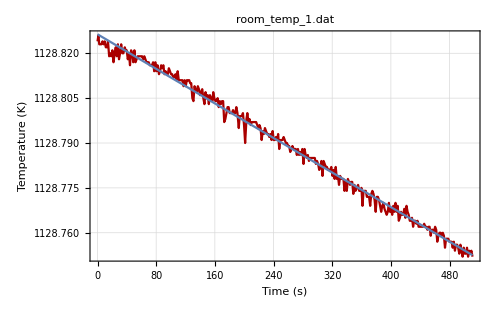
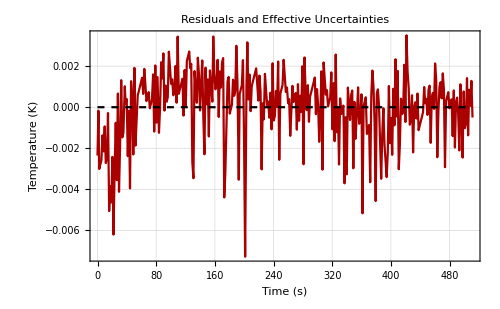
-Graphics-
-Graphics-
y(x) = a + b x
a= 
1128.83 | b= 
-0.000144437 | 
σ_a= 
0.000184814 | σ_b= 
6.25598×10^-7 | Std. deviation= 
0.00171335

```mathematica
LinearDifferencePlot[FrameLabel->{"Time (s)", "Temperature (K)"}]
```

```mathematica
errSemi=0.0017133548093589553;
```

This allows us to estimate the error in (doped) semiconductor resistance measurements as σ_R_semiconductor=0.0017 Ω.

### Uncertainty in resistance - copper resistor

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 24/room_temp_1.dat

File comment header:

Resistivity Experiment v3.0

Data Acquisition Unit: Agilent Model 34970A
Start Time: 1:38:51.915 PM 5/24/2018 ; Start Temp: 298.9860 K
Time (s)   Temp (K)         R1         R2         R3         R4         R5

Read 341 data points.

We use the standard deviation of the room temperature measurements of copper resistance fit to a linear model (again, it appears to adequately fit the data) to estimate the error in resistance measurements for copper. Note that we use the data of resistance as a function of time, not of temperature, to avoid correlation issues between the error in temperature determined above and the error in resistance as a function of temperature.

```mathematica
LinearFit[]
```

n = 341

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
5.65391 | b= 
-1.24902×10^-6 | 
σ_a= 
0.0000448065 | σ_b= 
1.5167×10^-7 | Std. deviation= 
0.000415383

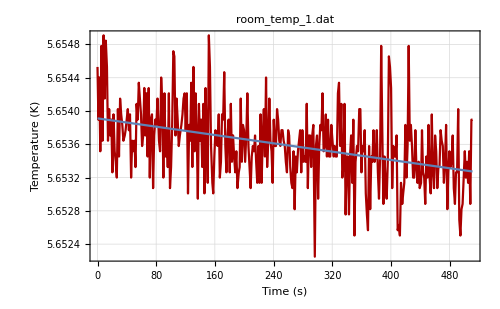
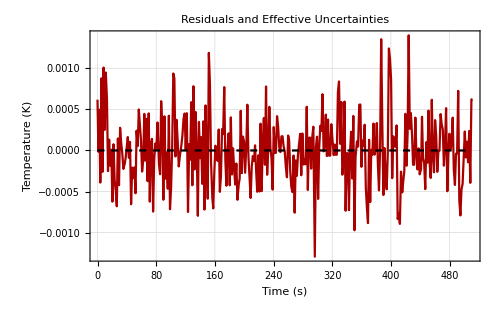
-Graphics-
-Graphics-
y(x) = a + b x
a= 
5.65391 | b= 
-1.24902×10^-6 | 
σ_a= 
0.0000448065 | σ_b= 
1.5167×10^-7 | Std. deviation= 
0.000415383

```mathematica
LinearDifferencePlot[FrameLabel->{"Time (s)", "Temperature (K)"}]
```

```mathematica
errCopper=0.00041538344072802603;
```

This allows us to estimate the error in copper resistance measurements as σ_R_copper=0.00042 Ω.

### Uncertainty in resistance - thermistor

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 24/room_temp_1.dat

File comment header:

Resistivity Experiment v3.0

Data Acquisition Unit: Agilent Model 34970A
Start Time: 1:38:51.915 PM 5/24/2018 ; Start Temp: 298.9860 K
Time (s)   Temp (K)         R1         R2         R3         R4         R5

Read 341 data points.

We use the standard deviation of the room temperature measurements of copper resistance fit to a quadratic model (again, it appears to adequately fit the data) to estimate the error in resistance measurements for copper. Note that we use the data of resistance as a function of time, not of temperature, to avoid correlation issues between the error in temperature determined above and the error in resistance as a function of temperature.

```mathematica
QuadraticFit[]
```

n = 341

y(x) = a + b x + c x^2

Fit of (x,y)  (unweighted)

a= 
39352. | b= 
0.150216 | c= 
-0.0000610126 | 
σ_a= 
0.122844 | σ_b= 
0.00111117 | σ_c= 
2.10555×10^-6 | Std. deviation= 
0.764792

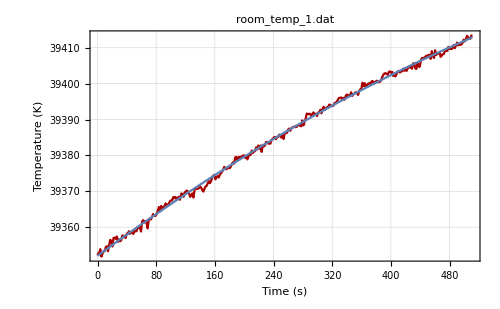
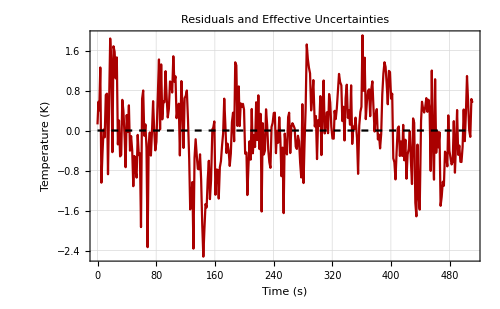
-Graphics-
-Graphics-
y(x) = a + b x + c x^2
a= 
39352. | b= 
0.150216 | c= 
-0.0000610126 | 
σ_a= 
0.122844 | σ_b= 
0.00111117 | σ_c= 
2.10555×10^-6 | Std. deviation= 
0.764792

```mathematica
LinearDifferencePlot[FrameLabel->{"Time (s)", "Temperature (K)"}]
```

```mathematica
errThermistor=0.7647923702705844;
```

This allows us to estimate the error in copper resistance measurements as σ_R_Thermistor=0.76 Ω.

## Resistance of copper with respect to temperature

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 24/heat_up.dat

File comment header:

Resistivity Experiment v3.0

Data Acquisition Unit: Agilent Model 34970A
Start Time: 2:34:01.712 PM 5/24/2018 ; Start Temp: 229.2230 K
Time (s)   Temp (K)         R1         R2         R3         R4         R5

Read 300 data points.

```mathematica
AssignYsigmas[ errCopper](* insert value between brackets *)
```

21 σy values replaced.

```mathematica
SwitchXXandYY[]
```

xx and yy have been switched (so have sx and sy).

```mathematica
AssignYsigmas[ errTemp](* insert value between brackets *)
```

21 σy values replaced.

```mathematica
SwitchXXandYY[]
```

xx and yy have been switched (so have sx and sy).

```mathematica
LinearFit[]
```

n = 300

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-0.874088 | b= 
0.0218298 | 
σ_a= 
0.000353685 | σ_b= 
1.14125×10^-6 | Std. deviation= 
0.000882905

Fit of (x,y±σ_y)

a= 
-0.874088 | b= 
0.0218298 | 
σ_a= 
0.0001664 | σ_b= 
5.36927×10^-7 | χ^2/(n-2)= 
4.51782

Fit of (x±σ_x,y±σ_y)

a= 
-0.874088 | b= 
0.0218298 | 
σ_a= 
0.000166589 | σ_b= 
5.37538×10^-7 | χ^2/(n-2)= 
4.50818

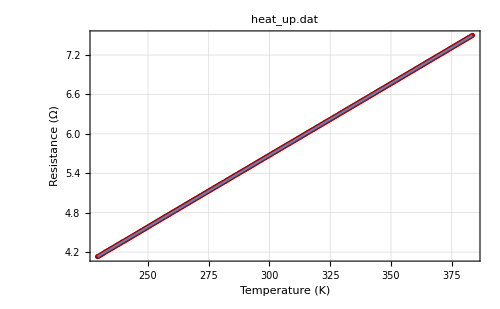
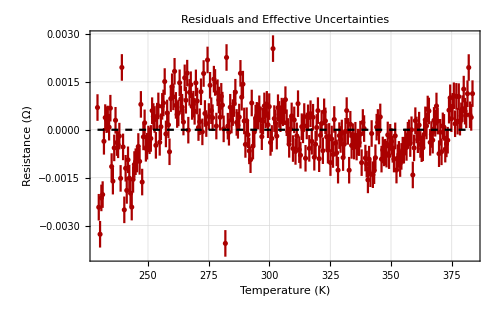
-Graphics-
-Graphics-
y(x) = a + b x
a= 
-0.874088 | b= 
0.0218298 | 
σ_a= 
0.000166589 | σ_b= 
5.37538×10^-7 | χ^2/(n-2)= 
4.50818

```mathematica
LinearDifferencePlot[FrameLabel->{"Temperature (K)", "Resistance (Ω)"}]
```

We observe a relatively good fit of the data to a linear model ((χ̃)^2=4.51), as expected from the theory presented in the lab manual. We perform the same fit over the overnight cool-down dataset (we will later use this to estimate the systematic uncertainties due to temperature gradients).

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 24/cool_down_overnight.dat

File comment header:

Resistivity Experiment v3.0

Data Acquisition Unit: Agilent Model 34970A
Start Time: 4:31:11.273 PM 5/24/2018 ; Start Temp: 383.5050 K
Time (s)   Temp (K)         R1         R2         R3         R4         R5

LoadFile::sorted: Data sorted in increasing x order.

Read 163 data points.

```mathematica
AssignYsigmas[ errCopper](* insert value between brackets *)
```

163 σy values replaced.

```mathematica
SwitchXXandYY[]
```

xx and yy have been switched (so have sx and sy).

```mathematica
AssignYsigmas[ errTemp](* insert value between brackets *)
```

163 σy values replaced.

```mathematica
SwitchXXandYY[]
```

xx and yy have been switched (so have sx and sy).

```mathematica
LinearFit[]
```

n = 163

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-0.874498 | b= 
0.0218324 | 
σ_a= 
0.00074672 | σ_b= 
2.17629×10^-6 | Std. deviation= 
0.000662819

Fit of (x,y±σ_y)

a= 
-0.874498 | b= 
0.0218324 | 
σ_a= 
0.000468012 | σ_b= 
1.36382×10^-6 | χ^2/(n-2)= 
2.54619

Fit of (x±σ_x,y±σ_y)

a= 
-0.874498 | b= 
0.0218324 | 
σ_a= 
0.000468538 | σ_b= 
1.36536×10^-6 | χ^2/(n-2)= 
2.54075

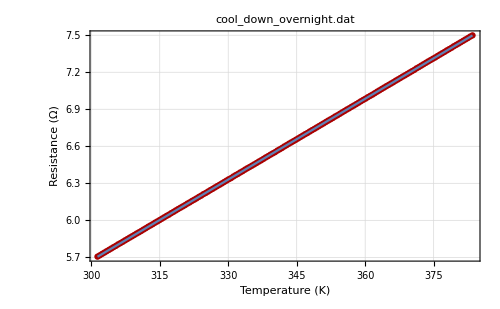
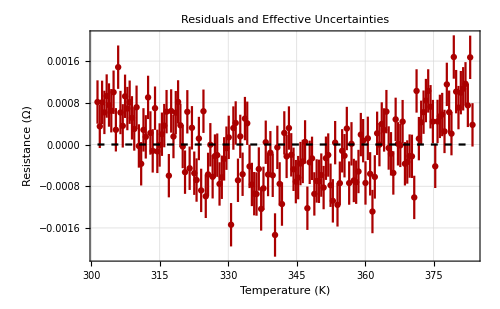
-Graphics-
-Graphics-
y(x) = a + b x
a= 
-0.874498 | b= 
0.0218324 | 
σ_a= 
0.000468538 | σ_b= 
1.36536×10^-6 | χ^2/(n-2)= 
2.54075

```mathematica
LinearDifferencePlot[FrameLabel->{"Temperature (K)", "Resistance (Ω)"}]
```

We now restrict our fit around 0°C and 20°C and use the fits to calculate the temperature coefficient of resistance, α.

### Estimating α_(20°C)

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{285.2,295.75}

n= 20

280 points removed.

```mathematica
LinearFit[]
```

n = 20

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-0.847052 | b= 
0.0217379 | 
σ_a= 
0.0143249 | σ_b= 
0.0000493144 | Std. deviation= 
0.000659638

Fit of (x,y±σ_y)

a= 
-0.847052 | b= 
0.0217379 | 
σ_a= 
0.0090206 | σ_b= 
0.0000310642 | χ^2/(n-2)= 
2.52181

Fit of (x±σ_x,y±σ_y)

a= 
-0.847052 | b= 
0.0217379 | 
σ_a= 
0.00903143 | σ_b= 
0.0000311015 | χ^2/(n-2)= 
2.51647

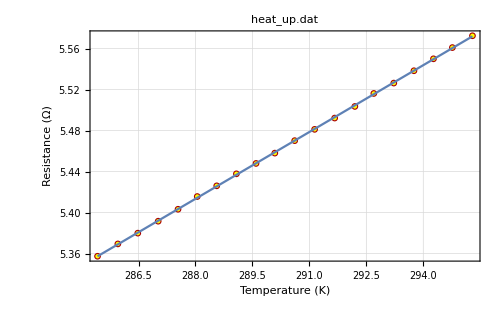
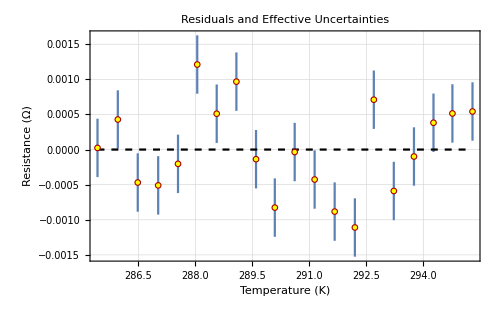
-Graphics-
-Graphics-
y(x) = a + b x
a= 
-0.847052 | b= 
0.0217379 | 
σ_a= 
0.00903143 | σ_b= 
0.0000311015 | χ^2/(n-2)= 
2.51647

```mathematica
LinearDifferencePlot[FrameLabel->{"Temperature (K)", "Resistance (Ω)"}]
```

We observe an even better fit of the data over this range than over the whole dataset.

```mathematica
ab20={-0.8470524979828181,0.021737859891715228};
```

```mathematica
tempCoeff[t0_]:=b/(a+b(t0)){1,Sqrt[(sigb/b)^2+(siga^2+(t0 sigb)^2)/(a+b (t0))^2]}
```

```mathematica
tempCoeff[293.15]
```

{0.00393417,0.0000107321}

```mathematica
alpha20=%58;
```

From this, we can estimate α_(20°C)=0.003934 ± 0.000011 (°C)^-1, which is in fact within error of the published value of 0.00393 (°C)^-1 (National Bureau of Standards Circular No. 31 (1914 Edition)).

### Estimating α_(0°C)

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{264.35,275.5}

n= 21

279 points removed.

```mathematica
LinearFit[]
```

n = 21

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-0.868654 | b= 
0.0218128 | 
σ_a= 
0.0125494 | σ_b= 
0.0000464856 | Std. deviation= 
0.000675334

Fit of (x,y±σ_y)

a= 
-0.868654 | b= 
0.0218128 | 
σ_a= 
0.00771887 | σ_b= 
0.0000286125 | χ^2/(n-2)= 
2.64326

Fit of (x±σ_x,y±σ_y)

a= 
-0.868654 | b= 
0.0218128 | 
σ_a= 
0.00772821 | σ_b= 
0.0000286472 | χ^2/(n-2)= 
2.63762

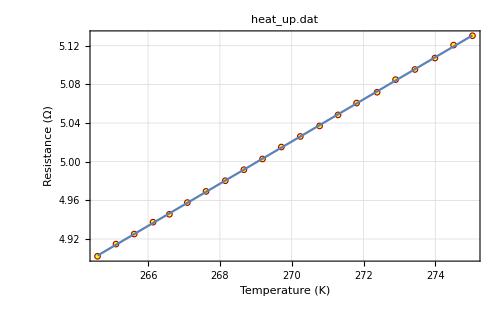
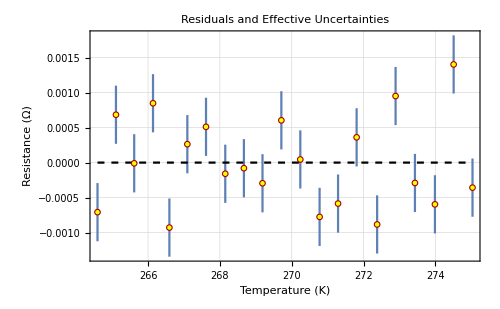
-Graphics-
-Graphics-
y(x) = a + b x
a= 
-0.868654 | b= 
0.0218128 | 
σ_a= 
0.00772821 | σ_b= 
0.0000286472 | χ^2/(n-2)= 
2.63762

```mathematica
LinearDifferencePlot[FrameLabel->{"Temperature (K)", "Resistance (Ω)"}]
```

```mathematica
ab0={-0.8686541861092515,0.021812845360786835};
```

Again, we observe an even better fit of the data over this range than over the whole dataset.

```mathematica
tempCoeff[273.15]
```

{0.00428583,0.0000108376}

```mathematica
alpha0=%240;
```

From this, we can estimate α_(20°C)=0.004286 ± 0.000011 (°C)^-1, which is in fact within error of the published value of 0.00428 (°C)^-1 (National Bureau of Standards Circular No. 31 (1914 Edition)).

## Resistance of thermistor (pure semiconductor) with respect to temperature

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 24/heat_up.dat

File comment header:

Resistivity Experiment v3.0

Data Acquisition Unit: Agilent Model 34970A
Start Time: 2:34:01.712 PM 5/24/2018 ; Start Temp: 229.2230 K
Time (s)   Temp (K)         R1         R2         R3         R4         R5

Read 300 data points.

We observe an offset in the first few points in the heat-up data, most likely caused by a hardware issue. We therefore disregard those points in our analysis.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{234.8,386.754}

n= 289

11 points removed.

```mathematica
AssignYsigmas[ errThermistor](* insert value between brackets *)
```

289 σy values replaced.

```mathematica
SwitchXXandYY[]
```

xx and yy have been switched (so have sx and sy).

```mathematica
AssignYsigmas[ errTemp](* insert value between brackets *)
```

289 σy values replaced.

```mathematica
SwitchXXandYY[]
```

xx and yy have been switched (so have sx and sy).

From the theory presented in the lab manual and our work from the pre-lab, we expect an exponential variation of resistance with inverse of temperature.

```mathematica
kb=1.3806*10^-23;
```

```mathematica
xnew[ x_, y_ ] := 1.0/(x)
ynew[ x_, y_ ] := y
DataTransform[]
(* Use Undo[] if you don't like the results. *)
```

All 289 points transformed.

```mathematica
SemilogCFit[]
```

n = 289

y(x) = a Exp[b x] + c

Fit of (x,y)  (unweighted)

a= 
0.272391 | b= 
3588.03 | c= 
-3065.12 | 
σ_a= 
0.00408646 | σ_b= 
3.57915 | σ_c= 
172.947 | Std. deviation= 
1917.35

Fit of (x,y±σ_y)

a= 
0.272388 | b= 
3588.04 | c= 
-3065.07 | 
σ_a= 
1.60586×10^-6 | σ_b= 
0.00143837 | σ_c= 
0.0523132 | χ^2/(n-3)= 
6.28517×10^6

Fit of (x±σ_x,y±σ_y)

a= 
0.146532 | b= 
3744.27 | c= 
-752.948 | 
σ_a= 
0.0000107457 | σ_b= 
0.0114185 | σ_c= 
0.150532 | χ^2/(n-3)= 
68004.1

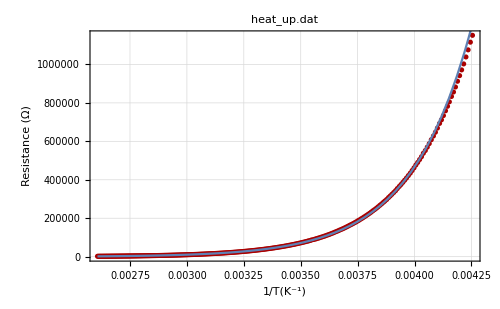
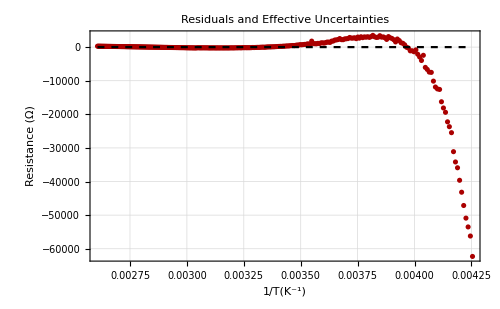
-Graphics-
-Graphics-
y(x) = a Exp[b x] + c
a= 
0.146532 | b= 
3744.27 | c= 
-752.948 | 
σ_a= 
0.0000107457 | σ_b= 
0.0114185 | σ_c= 
0.150532 | χ^2/(n-3)= 
68004.1

```mathematica
LinearDifferencePlot[FrameLabel->{"1/T(K^-1)","Resistance (Ω)"}]
```

We observe a very bad fit. This might indicate that the semiconductor is not as pure as we would expect. We remove the lower temperature values of our dataset and attempt the fit again.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.00257297,0.0034185}

n= 178

111 points removed.

```mathematica
SemilogCFit[]
```

n = 160

y(x) = a Exp[b x] + c

Fit of (x,y)  (unweighted)

a= 
0.00383148 | b= 
4825.76 | c= 
2459.4 | 
σ_a= 
3.35333 | σ_b= 
282.598 | σ_c= 
39.887 | Std. deviation= 
794.597

Fit of (x,y±σ_y)

Calculating sigc

a= 
0.0150364 | b= 
4417.85 | c= 
1413.71 | 
σ_a= 
0.67933 | σ_b= 
157.999 | σ_c= 
39.4428 | χ^2/(n-3)= 
350552.

Fit of (x±σ_x,y±σ_y)

a= 
0.080729 | b= 
3919.25 | c= 
-169.691 | 
σ_a= 
0.0000167373 | σ_b= 
0.518848 | σ_c= 
0.30351 | χ^2/(n-3)= 
421.105

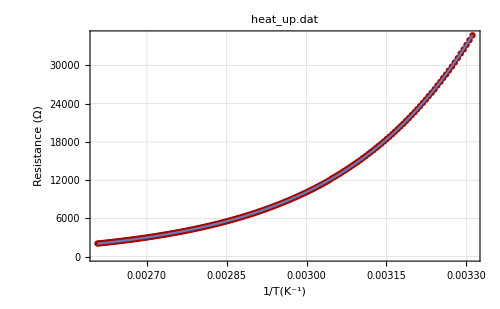
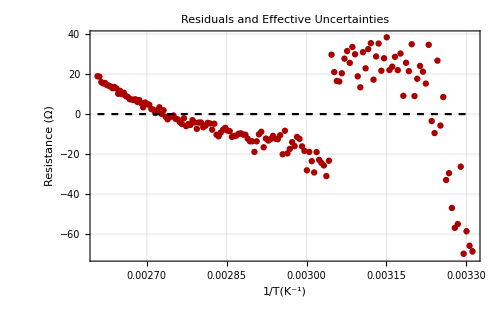
-Graphics-
-Graphics-
y(x) = a Exp[b x] + c
a= 
0.080729 | b= 
3919.25 | c= 
-169.691 | 
σ_a= 
0.0000167373 | σ_b= 
0.518848 | σ_c= 
0.30351 | χ^2/(n-3)= 
421.105

```mathematica
LinearDifferencePlot[FrameLabel->{"1/T(K^-1)","Resistance (Ω)"}]
```

This is a much better fit, as expected, but it is still relatively bad ((χ̃)^2=421) and the residuals still have a distinctive feature indicative either of an error in our model or of a measurement error. Since we need to reduce the range of temperatures to the high-temperature range to obtain a decent fit anyway, we may as well use the overnight cool-down dataset to minimize systematic errors due to temperature gradients.

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 24/cool_down_overnight.dat

File comment header:

Resistivity Experiment v3.0

Data Acquisition Unit: Agilent Model 34970A
Start Time: 4:31:11.273 PM 5/24/2018 ; Start Temp: 383.5050 K
Time (s)   Temp (K)         R1         R2         R3         R4         R5

LoadFile::sorted: Data sorted in increasing x order.

Read 163 data points.

As before, we observe the weird offset in the dataset at low temperatures, indicative of a hardware issue. We remove the offset portion of the dataset.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.00259272,0.0033088}

n= 161

2 points removed.

```mathematica
AssignYsigmas[ errThermistor](* insert value between brackets *)
```

163 σy values replaced.

```mathematica
SwitchXXandYY[]
```

xx and yy have been switched (so have sx and sy).

```mathematica
AssignYsigmas[ errTemp](* insert value between brackets *)
```

163 σy values replaced.

```mathematica
SwitchXXandYY[]
```

xx and yy have been switched (so have sx and sy).

From the theory presented in the lab manual and our work from the pre-lab, we expect an exponential variation of resistance with inverse of temperature.

```mathematica
kb=1.3806*10^-23;
```

```mathematica
xnew[ x_, y_ ] := 1.0/(x)
ynew[ x_, y_ ] := y
DataTransform[]
(* Use Undo[] if you don't like the results. *)
```

All 163 points transformed.

```mathematica
SemilogCFit[]
```

n = 163

y(x) = a Exp[b x] + c

Fit of (x,y)  (unweighted)

a= 
0.00368074 | b= 
4834.97 | c= 
2521.98 | 
σ_a= 
3.38478 | σ_b= 
280.666 | σ_c= 
36.8277 | Std. deviation= 
820.101

Fit of (x,y±σ_y)

a= 
0.0148334 | b= 
4419.42 | c= 
1461.52 | 
σ_a= 
0.696203 | σ_b= 
167.036 | σ_c= 
44.1802 | χ^2/(n-3)= 
380146.

Fit of (x±σ_x,y±σ_y)

a= 
0.0785559 | b= 
3925.67 | c= 
-129.672 | 
σ_a= 
0.00726604 | σ_b= 
16.1235 | σ_c= 
86.4626 | χ^2/(n-3)= 
630.075

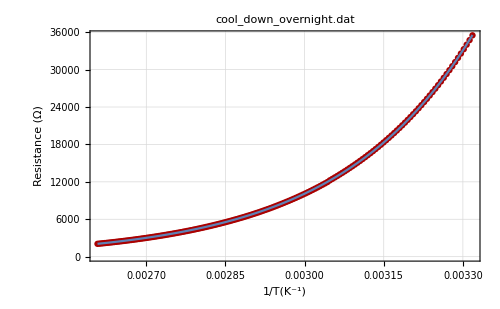
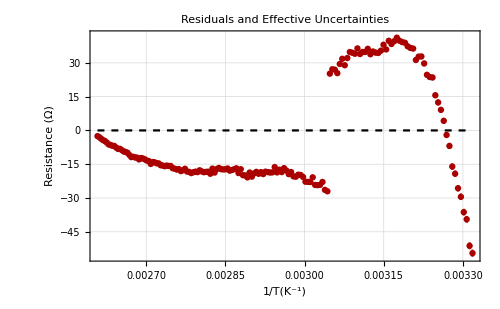
-Graphics-
-Graphics-
y(x) = a Exp[b x] + c
a= 
0.0785559 | b= 
3925.67 | c= 
-129.672 | 
σ_a= 
0.00726604 | σ_b= 
16.1235 | σ_c= 
86.4626 | χ^2/(n-3)= 
630.075

```mathematica
LinearDifferencePlot[FrameLabel->{"1/T(K^-1)","Resistance (Ω)"}]
```

We obtain a similarly bad fit, indicating that systematic errors due to temperature gradients are not the issue. By inspection of the structure of the residuals above, the error cannot correspond to a linear correction term, and therefore it would be difficult to correct for this issue by modifying the fitting function without knowing more about the nature of the discrepancy.

The structure of the residuals shown above, and the persistence of that structure over both datasets, however, indicates that the error may be due to the fact (c.f. Experiment 13) that E_g is non-constant with respect to temperature, contrary to what we assume in our model.

We simply use our best fit on the overnight cool-down data (to minimize temperature gradient systematic errors) to obtain an estimate of the gap energy in the thermistor’s semiconductor material from the fit parameters using R ∝ ⅇ^(E_g/(2 k_b T)).

```mathematica
eg=(2 kb)/(1.602*10^-19){3925.6724376520274,16.123484554446605} (* in eV *)
```

{0.676627,0.00277904}

We can therefore estimate E_g=0.6766 ± 0.0028 eV, which is within a couple standard errors of the expected value of 0.67 eV (note that we have yet to include systematic uncertainties).

## Resistance of semiconductor rod (doped semiconductor) with respect to temperature

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 24/heat_up.dat

File comment header:

Resistivity Experiment v3.0

Data Acquisition Unit: Agilent Model 34970A
Start Time: 2:34:01.712 PM 5/24/2018 ; Start Temp: 229.2230 K
Time (s)   Temp (K)         R1         R2         R3         R4         R5

Read 300 data points.

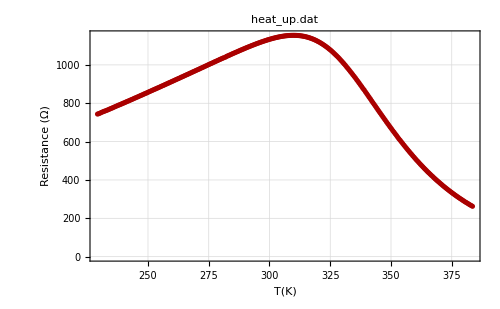

```mathematica
LinearDataPlot[FrameLabel->{"T(K)","Resistance (Ω)"}]
```

```mathematica
AssignYsigmas[ errSemi](* insert value between brackets *)
```

300 σy values replaced.

```mathematica
SwitchXXandYY[]
```

xx and yy have been switched (so have sx and sy).

```mathematica
AssignYsigmas[ errTemp](* insert value between brackets *)
```

300 σy values replaced.

```mathematica
SwitchXXandYY[]
```

xx and yy have been switched (so have sx and sy).

### Low-temperature behavior

We start by analyzing the asymptotic behavior at low temperatures, which should follow R ∝ T^(3/2)/N_d. For all following analysis, we algebraically modify our dataset so as to linearize the model we need to fit our data to. This approach is used in order to obtain a weighted fit (including a goodness-of-fit characteristic), because the fitting routines provided seem to be unable to fit to restricted datasets, and the full datasets fit very poorly to our models.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{235.13,269.44}

n= 66

37 points removed.

```mathematica
xnew[ x_, y_ ] := x 
ynew[ x_, y_ ] := y^(2/3)

DataTransform[]

(* Use Undo[] if you don't like the results. *)
```

All 300 points transformed.

```mathematica
LinearFit[]
```

n = 66

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-8.79105 | b= 
0.396099 | 
σ_a= 
0.0358592 | σ_b= 
0.000141944 | Std. deviation= 
0.0113541

Fit of (x,y±σ_y)

a= 
-8.79105 | b= 
0.396099 | 
σ_a= 
0.000350596 | σ_b= 
1.3854×10^-6 | χ^2/(n-2)= 
8897.88

Fit of (x±σ_x,y±σ_y)

a= 
-8.79105 | b= 
0.396099 | 
σ_a= 
0.0021289 | σ_b= 
8.4237×10^-6 | χ^2/(n-2)= 
947.463

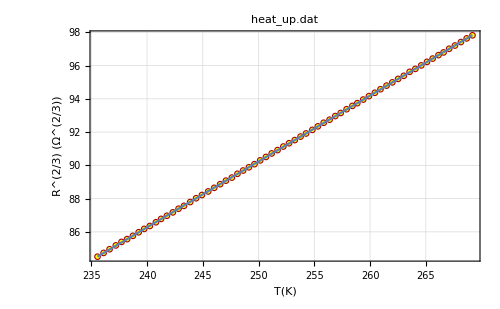
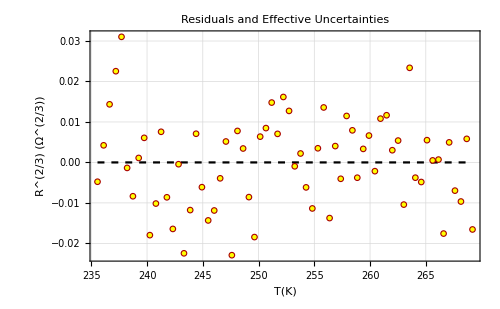
-Graphics-
-Graphics-
y(x) = a + b x
a= 
-8.79105 | b= 
0.396099 | 
σ_a= 
0.0021289 | σ_b= 
8.4237×10^-6 | χ^2/(n-2)= 
947.463

```mathematica
LinearDifferencePlot[FrameLabel->{"T(K)","R^(2/3) (Ω^(2/3))"}]
```

We obtain a bad fit even over a very restricted dataset, but the residuals have no apparent structure. This indicates the presence of a temperature-dependent source of error either in the temperature measurements or in the resistance measurements that the room-temperature measurements we have used to estimate noise have not allowed us to detect.

We now check for over-fitting by fitting the same dataset to a linear model.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{235.7,270.25}

n= 67

233 points removed.

```mathematica
LinearFit[]
```

n = 67

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-562.695 | b= 
5.68157 | 
σ_a= 
1.78118 | σ_b= 
0.00702885 | Std. deviation= 
0.574846

Fit of (x,y±σ_y)

a= 
-562.695 | b= 
5.68157 | 
σ_a= 
0.00530896 | σ_b= 
0.0000209497 | χ^2/(n-2)= 
112566.

Fit of (x±σ_x,y±σ_y)

a= 
-562.695 | b= 
5.68157 | 
σ_a= 
0.257234 | σ_b= 
0.0010147 | χ^2/(n-2)= 
11825.4

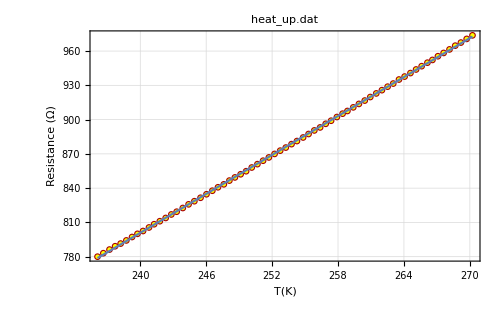
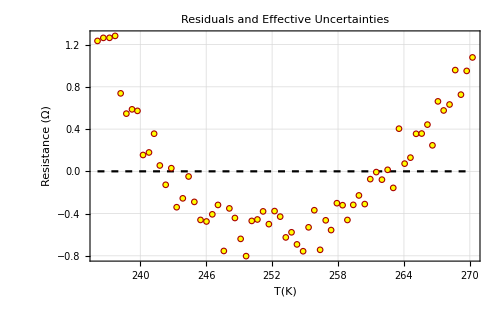
-Graphics-
-Graphics-
y(x) = a + b x
a= 
-562.695 | b= 
5.68157 | 
σ_a= 
0.257234 | σ_b= 
0.0010147 | χ^2/(n-2)= 
11825.4

```mathematica
LinearDifferencePlot[FrameLabel->{"T(K)","Resistance (Ω)"}]
```

As expected, we obtain a much worse fit to the linear model and a definite structure to our residuals, indicating that we have not been over-fitting a linear dataset (as it may appear to be at first glance) to a power-law model.

We now test for the presence of linear correction terms that may allow us to obtain a better fit by fitting a Log-Log of our data to a linear model (Log-Log will linearize any linear, polynomial, or exponential terms to our model).

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{5.46905,5.59975}

n= 64

38 points removed.

```mathematica
xnew[ x_, y_ ] := Log[x] 
ynew[ x_, y_ ] := Log[y]

DataTransform[]

(* Use Undo[] if you don't like the results. *)
```

All 67 points transformed.

```mathematica
LinearFit[]
```

n = 67

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-2.32533 | b= 
1.64428 | 
σ_a= 
0.00374079 | σ_b= 
0.000676051 | Std. deviation= 
0.000218618

Fit of (x,y±σ_y)

a= 
-2.32347 | b= 
1.64394 | 
σ_a= 
0.000033722 | σ_b= 
6.08843×10^-6 | χ^2/(n-2)= 
12540.2

Fit of (x±σ_x,y±σ_y)

a= 
-2.32423 | b= 
1.64408 | 
σ_a= 
0.000103808 | σ_b= 
0.0000187483 | χ^2/(n-2)= 
1312.54

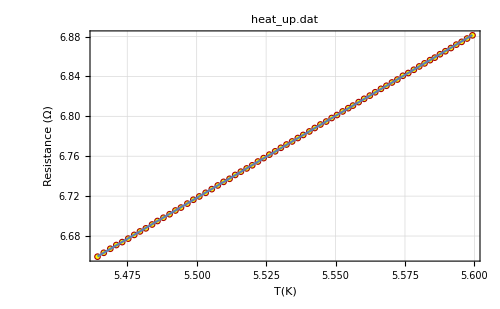
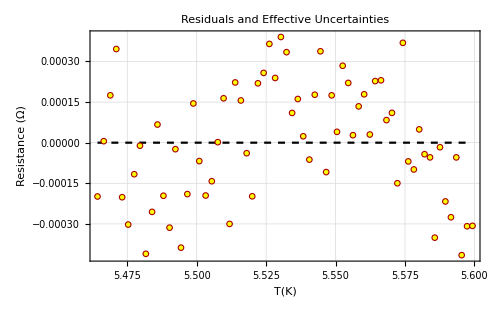
-Graphics-
-Graphics-
y(x) = a + b x
a= 
-2.32423 | b= 
1.64408 | 
σ_a= 
0.000103808 | σ_b= 
0.0000187483 | χ^2/(n-2)= 
1312.54

```mathematica
LinearDifferencePlot[FrameLabel->{"T(K)","Resistance (Ω)"}]
```

We do not obtain a significantly better fit that using the power-law model (in fact it is slightly worse), so we conclude that the bad-fit issue cannot be resolved by adding degrees of freedom (correction parameters) to our model. Therefore there must indeed be a source of error in the resistance and /or temperature measurements that the room-temperature data did not allow us to detect. This source of noise must then either be temperature-dependent or transient.

### High-temperature behavior

We now analyze the asymptotic behavior at high temperatures. At high temperatures, the charge carriers are principally intrinsic in nature, and resistance follows an exponential relationship to the inverse of temperature as it did for the pure semiconductor. We algebraically modify the dataset to linearize such a model and restrict our fits to linear regions of the modified dataset.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.00262685,0.00270425}

n= 21

11 points removed.

```mathematica
xnew[ x_, y_ ] := 1.0/x
ynew[ x_, y_ ] := Log[y]

DataTransform[]

(* Use Undo[] if you don't like the results. *)
```

All 66 points transformed.

```mathematica
LinearFit[]
```

n = 21

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-4.84986 | b= 
3997.73 | 
σ_a= 
0.0167868 | σ_b= 
6.29811 | Std. deviation= 
0.000629111

Fit of (x,y±σ_y)

a= 
-4.84045 | b= 
3994.2 | 
σ_a= 
0.00013845 | σ_b= 
0.051891 | χ^2/(n-2)= 
14089.2

Fit of (x±σ_x,y±σ_y)

a= 
-4.85165 | b= 
3998.4 | 
σ_a= 
0.000681282 | σ_b= 
0.255756 | χ^2/(n-2)= 
611.727

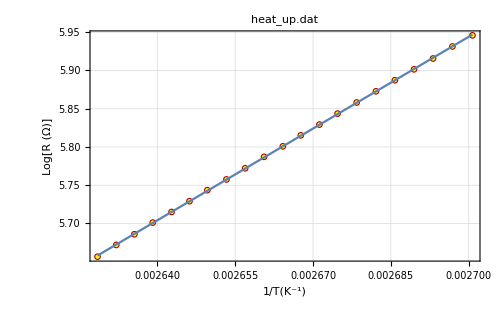
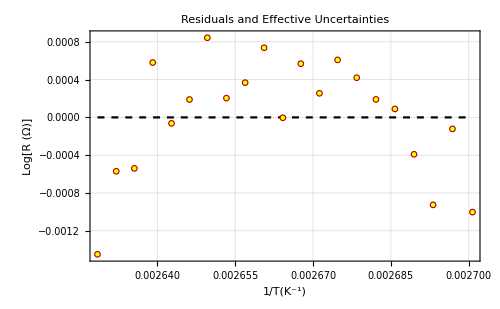
-Graphics-
-Graphics-
y(x) = a + b x
a= 
-4.85165 | b= 
3998.4 | 
σ_a= 
0.000681282 | σ_b= 
0.255756 | χ^2/(n-2)= 
611.727

```mathematica
LinearDifferencePlot[FrameLabel->{"1/T(K^-1)","Log[R (Ω)]"}]
```

Again we obtain a bad fit, with some structure remaining in the residuals.

We attempt the same approach for the overnight cool-down dataset in an attempt to minimize systematic errors due to temperature gradients (this dataset contains no asymptotic low-temperature behaviour, so we could not do that for the high-temperature behavior).

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 24/cool_down_overnight.dat

File comment header:

Resistivity Experiment v3.0

Data Acquisition Unit: Agilent Model 34970A
Start Time: 4:31:11.273 PM 5/24/2018 ; Start Temp: 383.5050 K
Time (s)   Temp (K)         R1         R2         R3         R4         R5

LoadFile::sorted: Data sorted in increasing x order.

Read 163 data points.

```mathematica
AssignYsigmas[ errSemi](* insert value between brackets *)
```

163 σy values replaced.

```mathematica
SwitchXXandYY[]
```

xx and yy have been switched (so have sx and sy).

```mathematica
AssignYsigmas[ errTemp](* insert value between brackets *)
```

163 σy values replaced.

```mathematica
SwitchXXandYY[]
```

xx and yy have been switched (so have sx and sy).

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.0026375,0.00271785}

n= 22

17 points removed.

```mathematica
xnew[ x_, y_ ] := 1.0/x
ynew[ x_, y_ ] := Log[y]

DataTransform[]

(* Use Undo[] if you don't like the results. *)
```

All 163 points transformed.

```mathematica
LinearFit[]
```

n = 22

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-4.75635 | b= 
3962.28 | 
σ_a= 
0.0146495 | σ_b= 
5.46779 | Std. deviation= 
0.000594909

Fit of (x,y±σ_y)

a= 
-4.74622 | b= 
3958.5 | 
σ_a= 
0.000121465 | σ_b= 
0.0452967 | χ^2/(n-2)= 
15056.9

Fit of (x±σ_x,y±σ_y)

a= 
-4.75817 | b= 
3962.96 | 
σ_a= 
0.000627943 | σ_b= 
0.234595 | χ^2/(n-2)= 
541.948

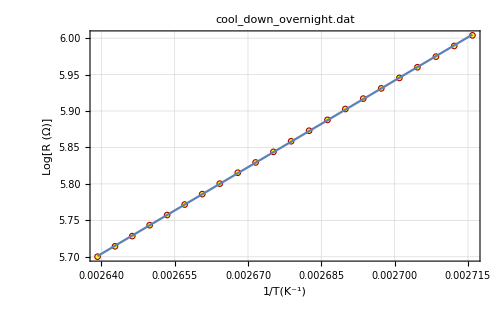
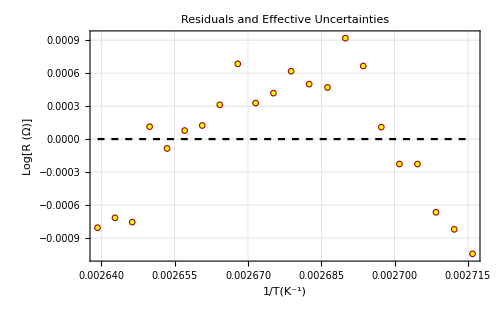
-Graphics-
-Graphics-
y(x) = a + b x
a= 
-4.75817 | b= 
3962.96 | 
σ_a= 
0.000627943 | σ_b= 
0.234595 | χ^2/(n-2)= 
541.948

```mathematica
LinearDifferencePlot[FrameLabel->{"1/T(K^-1)","Log[R (Ω)]"}]
```

We only obtain a slightly better fit, again indicating that temperature gradients are not the issue. Again, there is some structure to the residuals, indicative of a temperature-dependent source of error in either temperature or resistance measurements, or as a correction term in our model. Given the temperature range and behavior we are investigating, this could be as suggested in the analysis of the pure semiconductor, due to the variation of E_g with temperature.

Nevertheless, we use our best fit parameters to estimate the energy gap of the doped semiconductor.

```mathematica
egDoped=(2 kb)/(1.602*10^-19){3962.9602891968248,0.23459536880888965} (* in eV *)
```

{0.683054,0.0000404348}

Therefore, we estimate E_g=0.68305 ± 0.00004 eV for the energy gap of the doped semiconductor. While this is not quite within error of the expected energy gap for Germanium, and keeping in mind that we have yet to consider systematic uncertainties in our parameters, this is close enough to confidently conclude that the doped semiconductor is made of Germanium.

### Estimating the dopant fraction

We know that the curves for asymptotic behavior of resistance at low temperatures and high temperatures (respectively going to T^(3/2) and to ⅇ^(E_g/(2 k_b T))) intersect when N_d=2 n_(i.) We therefore use the intersection of lines on a Log-Log of our dataset to solve for the temperature at which this is the case. We then used the variation of n_i with temperature given in the lab manual (and used several times above) along with the value of n_i/N at room temperature (300 K) to find n_i/N at that temperature, and hence solve for N_d/(N.)=2 n_i/N

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 24/heat_up.dat

File comment header:

Resistivity Experiment v3.0

Data Acquisition Unit: Agilent Model 34970A
Start Time: 2:34:01.712 PM 5/24/2018 ; Start Temp: 229.2230 K
Time (s)   Temp (K)         R1         R2         R3         R4         R5

Read 300 data points.

```mathematica
AssignYsigmas[ errSemi](* insert value between brackets *)
```

300 σy values replaced.

```mathematica
SwitchXXandYY[]
```

xx and yy have been switched (so have sx and sy).

```mathematica
AssignYsigmas[ errTemp](* insert value between brackets *)
```

300 σy values replaced.

```mathematica
SwitchXXandYY[]
```

xx and yy have been switched (so have sx and sy).

```mathematica
xnew[ x_, y_ ] := Log[x] 
ynew[ x_, y_ ] := Log[y] 

DataTransform[]

(* Use Undo[] if you don't like the results. *)
```

All 300 points transformed.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{5.48375,5.55835}

n= 37

22 points removed.

```mathematica
LinearFit[]
```

n = 37

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-2.35241 | b= 
1.64919 | 
σ_a= 
0.00726253 | σ_b= 
0.0013153 | Std. deviation= 
0.000177206

Fit of (x,y±σ_y)

a= 
-2.3515 | b= 
1.64903 | 
σ_a= 
0.0000820634 | σ_b= 
0.0000148574 | χ^2/(n-2)= 
7844.19

Fit of (x±σ_x,y±σ_y)

a= 
-2.35201 | b= 
1.64912 | 
σ_a= 
0.000251959 | σ_b= 
0.0000456213 | χ^2/(n-2)= 
831.509

```mathematica
a1={-2.352008390458569,0.00025195861243940506};
b1={1.6491193023567654,0.000045621347718602734};
```

```mathematica
Undo[]
```

heat_up.dat

n = 300

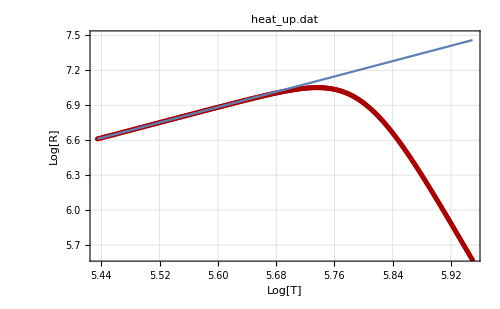
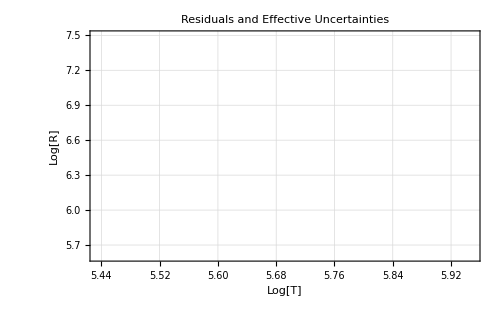
-Graphics-
-Graphics-
y(x) = a + b x
a= 
-2.35201 | b= 
1.64912 | 
σ_a= 
0.000251959 | σ_b= 
0.0000456213 | χ^2/(n-2)= 
831.509

```mathematica
LinearDifferencePlot[FrameLabel->{"Log[T]","Log[R]"},PlotRange->{Automatic,{5.6,7.5}}]
```

```mathematica
plt1=-Graphics-;
```

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{5.89834,5.92031}

n= 16

15 points removed.

```mathematica
LinearFit[]
```

n = 16

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
67.8551 | b= 
-10.4678 | 
σ_a= 
0.132623 | σ_b= 
0.0224426 | Std. deviation= 
0.000582378

Fit of (x,y±σ_y)

a= 
67.8167 | b= 
-10.4613 | 
σ_a= 
0.000973175 | σ_b= 
0.000164709 | χ^2/(n-2)= 
19052.7

Fit of (x±σ_x,y±σ_y)

a= 
67.8611 | b= 
-10.4689 | 
σ_a= 
0.00579526 | σ_b= 
0.00098069 | χ^2/(n-2)= 
526.407

```mathematica
a2={67.861086558961,0.005795255742176451};
b2={-10.468855441210536,0.0009806895850823203};
```

```mathematica
Undo[]
```

heat_up.dat

n = 300

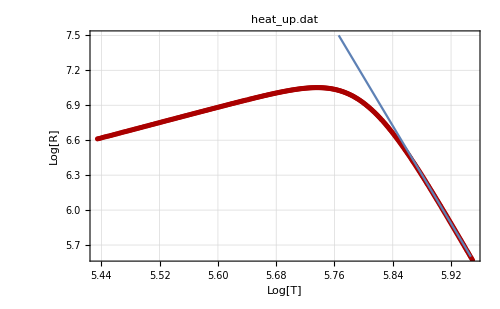
-Graphics-
-Graphics-
y(x) = a + b x
a= 
67.8611 | b= 
-10.4689 | 
σ_a= 
0.00579526 | σ_b= 
0.00098069 | χ^2/(n-2)= 
526.407

```mathematica
LinearDifferencePlot[FrameLabel->{"Log[T]","Log[R]"},PlotRange->{Automatic,{5.6,7.5}}]
```

```mathematica
plt2=-Graphics-;
```

Here is a plot of the intersection of our fits to the asymptotic models. We define the appropriate functions to calculate the intersection temperature T (K) from the fit parameters above, and use this to calculate N_d/N.

```mathematica
ImageCompose[plt1,plt2]
```

-Graphics-

```mathematica
intersection[a1_,b1_,a2_,b2_]:=(b2[[1]]-b1[[1]])/(a1[[1]]-a2[[1]]){1,Sqrt[(b1[[2]]^2+b2[[2]]^2)/(b2[[1]]-b1[[1]])^2+(a1[[2]]^2+a2[[2]]^2)/(a1[[1]]-a2[[1]])^2]};
```

```mathematica
int=intersection[b1,a1,b2,a2];
```

```mathematica
temp=ⅇ^int
```

{328.366,1.00067}

```mathematica
<<SimpleErrorPropagation`
```

```mathematica
?PropagateUncertainties
```

PropagateUncertainties[func, vars] propagates uncertainties in variables listed in vars = {variable1, variable2,...} and retuns the propagated uncertainty in func.
func must necessarily be differentiable with respect to all variables in vars, and the uncertainties in variables in vars must be independent.

It will return an algebraic expression in terms of the variables in vars, with uncertainty in some variable denoted by sigmaVariable.
It can be used either by providing an algebraic expression, then substituting values for the variables and uncertainties in a subsequent operation, or simply by assigning values and uncertainties to each variable using the naming conventions mentioned. In the latter case, it will be necessary to localize the variables in vars using Module or Block.

Note: Loading SimpleErrorPropagation` clears any variables named 'variance', 'varianceList' or 'PropagateUncertainties' due to function and subfunction names in the Package.

```mathematica
prop[t_]:=((5.4*10^-10) t^(3/2) ⅇ^(-0.67*1.602*10^-19/(2 kb t)))/(300^(3/2)ⅇ^(-0.67*1.602*10^-19/(2 kb 300)))
```

```mathematica
PropagateUncertainties[prop[t],{t}]//Simplify
```

6.60898×10^-8 √((ⅇ^(-7774.45/t) sigmaT^2 (2591.48+1. t)^2)/t)

```mathematica
prop2[t_,sigmaT_]:={prop[t],6.60898433030618*^-8 √((ⅇ^(-7774.445893089961/t) sigmaT^2 (2591.4819643633205+1. t)^2)/t)};
```

```mathematica
niFrac=prop2[temp[[1]],temp[[2]]];
```

```mathematica
npFrac=2 niFrac
```

{3.78785×10^-9,1.53964×10^-10}

Therefore we can estimate N_d/N=(3.79 ± 0.15)×10^-9 as the doping concentration for our sample.

## Systematic uncertainties

### Due to temperature gradients

We observe that the only dataset with a good enough fit to provide us with a reliable estimate of the offset in temperature (systematic error) caused by temperature gradients in the dielectric fluid is the copper resistance data. However, the linear offset parameters are within error of each other, making it difficult to infer a temperature offset from a comparison of the heat-up and overnight cool-down data (the latter should be relatively free of such temperature gradients).

Therefore, we simply obtain an upper bound for the magnitude of the systematic error by doubling the standard deviation of a linear fit to the combined heat-up and overnight cool-down datasets for temperature against copper resistance (as opposed to our previous fits of resistance against temperature).

#### Merging datasets

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 24/heat_up.dat

File comment header:

Resistivity Experiment v3.0

Data Acquisition Unit: Agilent Model 34970A
Start Time: 2:34:01.712 PM 5/24/2018 ; Start Temp: 229.2230 K
Time (s)   Temp (K)         R1         R2         R3         R4         R5

Read 300 data points.

```mathematica
With[  {name = SystemDialogInput["FileSave", DataFileName]},
  If[ name =!= $Canceled, SaveFile[name]]
]
```

Sorted data saved in /home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 24/heat_up_copper.dat

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 24/cool_down_overnight.dat

File comment header:

Resistivity Experiment v3.0

Data Acquisition Unit: Agilent Model 34970A
Start Time: 4:31:11.273 PM 5/24/2018 ; Start Temp: 383.5050 K
Time (s)   Temp (K)         R1         R2         R3         R4         R5

LoadFile::sorted: Data sorted in increasing x order.

Read 163 data points.

```mathematica
With[  {name = SystemDialogInput["FileSave", DataFileName]},
  If[ name =!= $Canceled, SaveFile[name]]
]
```

Sorted data saved in /home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 24/cool_down_copper.dat

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, MergeFile -> True]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 24/heat_up_copper.dat

300 data points merged from data set heat_up_copper.dat
total data: 463 points.

```mathematica
(* Remove the section of the merged dataset with no cool-down data *)
```

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{6.004,7.476}

n= 263

200 points removed.

```mathematica
(* Perform linear fit *)
```

```mathematica
LinearFit[]
```

n = 263

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
40.2118 | b= 
45.783 | 
σ_a= 
0.0300577 | σ_b= 
0.00445253 | Std. deviation= 
0.03055

#### Estimating error from standard deviation

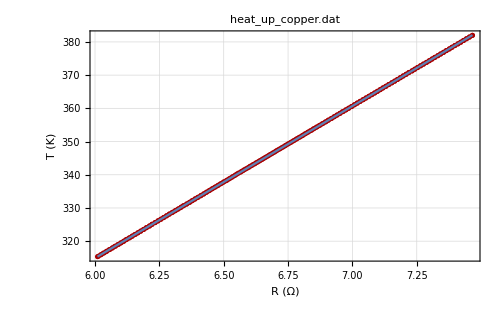
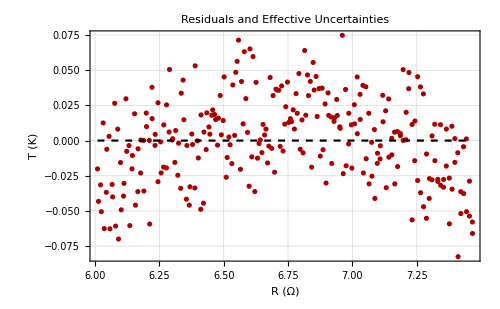
-Graphics-
-Graphics-
y(x) = a + b x
a= 
40.2118 | b= 
45.783 | 
σ_a= 
0.0300577 | σ_b= 
0.00445253 | Std. deviation= 
0.03055

```mathematica
LinearDifferencePlot[FrameLabel->{"R (Ω)","T (K)"}]
```

```mathematica
gradErr=2(0.030550010541453718);
```

### Due to temperature probe calibration

According to the probe data sheet, the maximum admissible error for the temperature measured is of the order of 0.37 K for our temperature range.

```mathematica
calErr=0.37;
```

Therefore the total systematic error in temperature is found by adding in quadrature:

```mathematica
sysTempErr=Sqrt[calErr^2+gradErr^2]
```

0.375011

So the systematic error in temperature is of the order of 0.38 K.

### Due to resistance measurement calibration

#### Copper

Using the accuracy specifications on pg 326 of the Agilent 39470A’s user manual, we can calculate:

```mathematica
errResCopper=((0.0030+0.0006)*10)+((0.0035+0.0005)*100)/100 (* in Ω *)
```

0.04

#### Pure semiconductor (thermistor)

```mathematica
errResThermistor=((0.002+0.0006)*4*10^4+(0.0005+0.0001)*10^4)/100 (* in Ω *)
```

1.1

#### Doped semiconductor

```mathematica
errDoped=(0.002+0.0006+0.0006+0.0001)*10^3/100 (* in Ω *)
```

0.033

## Parameter estimates for samples (including systematic uncertainties)

### Temperature coefficient of resistance

Recall that in terms of fit parameters and temperature T, α=b/(a+b(T)). Then a systematic error in R corresponds to introducing an error in a, so that the uncertainty in α is given by:

```mathematica
PropagateUncertainties[b/(a+b T),{a,T}]//Simplify
```

√((b^2 (sigmaA^2+b^2 sigmaT^2))/(a+b T)^4)

```mathematica
finalAlpha0={alpha0[[1]],alpha0[[2]],alpha0[[1]]^2 Sqrt[(errResCopper/ab0[[2]])^2+sysTempErr^2]}
```

{0.00428583,0.0000108376,0.0000343807}

```mathematica
finalAlpha20={alpha20[[1]],alpha20[[2]],alpha20[[1]]^2 Sqrt[(errResCopper/ab20[[2]])^2+sysTempErr^2]}
```

{0.00393417,0.0000107321,0.000029066}

### Gap energy

Observe that the logarithmic operation on the data to linearize the intrinsic charge carrier datasets (pure semiconductor or doped at high temperature) discards any effect of a systematic error in resistance. Therefore we only need to worry about the systematic error induced in the gap energies by the systematic error in temperature. Given the linear relationship between the fit parameter b and the gap energy, the systematic error in the gap energy should then simply be the gap energy scaled by the fractional systematic error in 1/T. We obtain an upper bound on the error simply by taking T to be the lowest temperature in our dataset.

```mathematica
finalEgPure={eg[[1]],eg[[2]],sysTempErr/230 eg[[1]]}
```

{0.676627,0.00277904,0.00110323}

```mathematica
finalEgDoped={egDoped[[1]],egDoped[[2]],sysTempErr/370 egDoped[[1]]}
```

{0.683054,0.0000404348,0.000692305}

### Doping fraction

Observe that the Log-Log operation and solving for the asymptotic intersection temperature discards any systematic error in resistance (whether a scaling or an offset), and introduces an error in the intersection temperature in accordance with the systematic error in T, as expected. Therefore we simply propagate the uncertainty in T as before, but this time consider the systematic uncertainty in T.

```mathematica
finalNp={npFrac[[1]],npFrac[[2]],2 prop2[temp[[1]],sysTempErr][[2]]}
```

{3.78785×10^-9,1.53964×10^-10,5.76995×10^-11}

## Final parameter estimates

```mathematica
param={{"Sample","Parameter","Estimate"},{"Copper","α_(0  °C) ((°C)^-1)","0.004286 ± 0.000011 ± 0.000029"},{"Copper","α_(20  °C) ((°C)^-1)","0.003934 ± 0.000011 ± 0.000029"},{"Thermistor","E_g (eV)","0.6766 ± 0.0028 ± 0.0011"},{"Doped Semiconductor","E_g (eV)","0.68305 ± 0.00004 ± 0.00069"},{"Doped Semiconductor","N_p/N","(3.79 ± 0.15 ± 0.06) × 10^-9"}};
```

```mathematica
Grid[param,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]
```

Sample | Parameter | Estimate
Copper | α_(0  °C) ((°C)^-1) | 0.004286 ± 0.000011 ± 0.000029
Copper | α_(20  °C) ((°C)^-1) | 0.003934 ± 0.000011 ± 0.000029
Thermistor | E_g (eV) | 0.6766 ± 0.0028 ± 0.0011
Doped Semiconductor | E_g (eV) | 0.68305 ± 0.00004 ± 0.00069
Doped Semiconductor | N_p/N | (3.79 ± 0.15 ± 0.06) × 10^-9

## Other resistors

### Manganin wire

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 24/heat_up.dat

File comment header:

Resistivity Experiment v3.0

Data Acquisition Unit: Agilent Model 34970A
Start Time: 2:34:01.712 PM 5/24/2018 ; Start Temp: 229.2230 K
Time (s)   Temp (K)         R1         R2         R3         R4         R5

Read 300 data points.

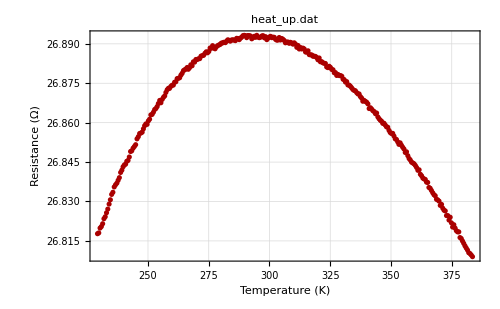

```mathematica
LinearDataPlot[FrameLabel->{"Temperature (K)","Resistance (Ω)"}]
```

### Commercial resistor

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 24/heat_up.dat

File comment header:

Resistivity Experiment v3.0

Data Acquisition Unit: Agilent Model 34970A
Start Time: 2:34:01.712 PM 5/24/2018 ; Start Temp: 229.2230 K
Time (s)   Temp (K)         R1         R2         R3         R4         R5

Read 300 data points.

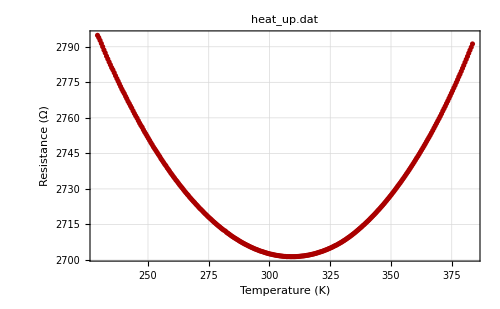

```mathematica
LinearDataPlot[FrameLabel->{"Temperature (K)","Resistance (Ω)"}]
```

In both cases, we observe a very small fractional change in resistance over our temperature range. Furthermore, they both have a stationary point near room temperature. This appears to be by design, seeing that this ensures that resistance is essentially constant (the derivative of resistance with respect to temperature vanishes near the stationary point) over a range of operating temperatures which we of course expect to be around room temperature. This is essential to ensure proper functioning of devices using these components as resistors (we want the resistance to be as rated at room temperature and remain unchanged over a range of reasonable working temperatures to account for temperature fluctuations and self-heating).